```mathematica
(*1. 基础参数设置*)
a0=3.3697998668513285;(*晶格常数*)

(*2. 12d 原子坐标 (分数坐标)*)
hFracPos={
{0.25,0.00,0.50},{0.25,0.50,0.00},{0.50,0.25,0.00},
{0.00,0.25,0.50},{0.50,0.00,0.75},{0.00,0.50,0.75},
{0.75,0.50,0.00},{0.75,0.00,0.50},{0.00,0.75,0.50},
{0.50,0.75,0.00},{0.00,0.50,0.25},{0.50,0.00,0.25}
};
hCartPos=hFracPos*a0;
nAtoms=Length[hFracPos];

(*Slater-Koster 跳跃积分参数 (eV)*)
eS=-5.0;(*s 轨道能量*)
eP=2.0;(*p 轨道能量*)
vssSigma=-1.40;
vspSigma=1.80;(*s 到 p 的 sigma 跳跃*)
vppSigma=2.20;(*p 到 p 的 sigma 跳跃*)
vppPi=-0.35;(*p 到 p 的 pi 跳跃*)
nOrbitals=4;(*s,px,py,pz*)
dim=nAtoms*nOrbitals;(*矩阵总维度为 48*)
```

```mathematica
(*2. 定义 Slater-Koster 跳跃函数*)
(*这是最关键的部分。两个原子之间的跳跃不再是一个常数 $t1$，而是取决于它们之间连线方向的余弦值 $(l,m,n)$。*)
(*定义 4x4 的 SK 跳跃子矩阵*)
SKBlock[distVec_,dist_]:=Module[
{l,m,n,mat},{l,m,n}=distVec/dist;(*方向余弦*)
mat=ConstantArray[0,{4,4}];
(*这里的索引 1:s,2:px,3:py,4:pz*)(*s-s*)
mat[[1,1]]=vssSigma;
(*s-p (注意：i到j和j到i的正负号)*)
mat[[1,2]]=l*vspSigma;
mat[[1,3]]=m*vspSigma;
mat[[1,4]]=n*vspSigma;
(*p-s (根据对称性，s到p和p到s差一个负号)*)
mat[[2,1]]=-l*vspSigma;
mat[[3,1]]=-m*vspSigma;
mat[[4,1]]=-n*vspSigma;
(*p-p*)
mat[[2,2]]=l^2*vppSigma+(1-l^2)*vppPi;
mat[[2,3]]=l*m*(vppSigma-vppPi);
mat[[2,4]]=l*n*(vppSigma-vppPi);
mat[[3,2]]=m*l*(vppSigma-vppPi);
mat[[3,3]]=m^2*vppSigma+(1-m^2)*vppPi;
mat[[3,4]]=m*n*(vppSigma-vppPi);
mat[[4,2]]=n*l*(vppSigma-vppPi);
mat[[4,3]]=n*m*(vppSigma-vppPi);
mat[[4,4]]=n^2*vppSigma+(1-n^2)*vppPi;
mat];
```

```mathematica
(*3. 寻找最近邻 (包含跨胞跳跃)*)
(*距离阈值设定为 a*sqrt(2)/4 附近*)
cutoff=1.2;
neighbors={};
Do[
Do[
distVec=(hCartPos[[j]]+{dx,dy,dz}*a0)-hCartPos[[i]];
dist=Norm[distVec];
If[0.1<dist<cutoff,
 (*`dist>0.1：排除掉“自己跳向自己”的情况*)
(*`dist<cutoff`这是紧束缚模型的关键，假设电子只能跳到很近的原子上，氢笼的最近邻距离大约是 $1.24$ Å，所以我们设置 cutoff=1.3。只有距离小于 1.3 的原子对才会被认为有“跳跃（Hopping）”发生。*)
AppendTo[neighbors,{i,j,{dx,dy,dz}}]
],
{i,nAtoms},{j,nAtoms}],
{dx,-1,1},{dy,-1,1},{dz,-1,1}
];
(*Do[Print["dx: ",dx,"  dy: ",dy,"  dz: ",dz],{dx,-1,1},{dy,-1,1},{dz,-1,1}] 可以用来理解Do的三重循环*)
adjMatrix=ConstantArray[0,{nAtoms,nAtoms}];
(*遍历找到的邻居列表，将对应位置设为 1*)
Do[
iIdx=neighbors[[idx,1]];
jIdx=neighbors[[idx,2]];
adjMatrix[[iIdx,jIdx]]=1,
{idx,Length[neighbors]}
];
(*4. 邻接矩阵展示*)
Print["--- 基于周期性边界条件的邻接矩阵 ---"];
Print["(1 表示在 1.3 Å 范围内存在跳跃路径)"];
adjMatrix//MatrixForm
Total[adjMatrix,{2}]//Print
(*5. 验证配位数*)
Print["每个原子的实际配位数 (邻接矩阵每行求和):"];
Total[adjMatrix,{2}]//Print
(*6. 打印具体的连接关系*)
Print["详细连接关系 (i -> j):"];
Table[
"H"<>ToString[i]<>" 可以跳向 -> "<>StringRiffle[Table["H"<>ToString[j],{j,Flatten[Position[adjMatrix[[i]],1]]}],", "],{i,nAtoms} ]//Column
```

--- 基于周期性边界条件的邻接矩阵 ---

(1 表示在 1.3 Å 范围内存在跳跃路径)

(0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0)

{4,4,4,4,4,4,4,4,4,4,4,4}

每个原子的实际配位数 (邻接矩阵每行求和):

{4,4,4,4,4,4,4,4,4,4,4,4}

详细连接关系 (i -> j):

H1 可以跳向 -> H4, H5, H9, H12
H2 可以跳向 -> H3, H6, H10, H11
H3 可以跳向 -> H2, H5, H7, H12
H4 可以跳向 -> H1, H6, H8, H11
H5 可以跳向 -> H1, H3, H8, H10
H6 可以跳向 -> H2, H4, H7, H9
H7 可以跳向 -> H3, H6, H10, H11
H8 可以跳向 -> H4, H5, H9, H12
H9 可以跳向 -> H1, H6, H8, H11
H10 可以跳向 -> H2, H5, H7, H12
H11 可以跳向 -> H2, H4, H7, H9
H12 可以跳向 -> H1, H3, H8, H10

```mathematica
(*4. 构造哈密顿矩阵 H(kx,ky,kz)*)
```

```mathematica
Ham[kx_,ky_,kz_]:=Module[
{H,kVec,phase,i,j,R,distVec,dist,hopBlock},
H=ConstantArray[0,{dim,dim}];
kVec={kx,ky,kz};

(*A.填充在位能 (对角块)*)
Do[
H[[(i-1)*4+1,(i-1)*4+1]]=eS;
H[[(i-1)*4+2,(i-1)*4+2]]=eP;
H[[(i-1)*4+3,(i-1)*4+3]]=eP;
H[[(i-1)*4+4,(i-1)*4+4]]=eP;,{i,nAtoms}
];

(*B.填充跳跃项*)
Do[
i=neighbors[[idx,1]];
j=neighbors[[idx,2]];
R=neighbors[[idx,3]];
(*计算实空间的位移向量*)
distVec=(hCartPos[[j]]+R*a0)-hCartPos[[i]];
dist=Norm[distVec];
(*获取 4x4 跳跃矩阵*)
hopBlock=SKBlock[distVec,dist];
phase=Exp[I*2*Pi*(kVec.R)];
(*将 4x4 块放入 48x48 矩阵中*)
Do[
Do[
H[[(i-1)*4+row,(j-1)*4+col]]+=hopBlock[[row,col]]*phase;,
{col,4}
],
{row,4}
];,

{idx,Length[neighbors]}];
H];
```

```mathematica
(*5. 能带路径设置 (G-X-M-G-R)*)
pathPoints={
{0,0,0},(*G*)
{0,0.5,0},(*X*)
{0.5,0.5,0},(*M*)
{0,0,0},(*G*)
{0.5,0.5,0.5},(*R*)
{0,0.5,0} (*X*)
};
labels={"Γ","X","M","Γ","R", "X"};
segments=100;(*每段采点数*)
(*在高对称点之间进行线性插值，生成一条连续的 $k$ 空间采样路径。*)
kPath=Flatten[Table[
Table[pathPoints[[i]]+(pathPoints[[i+1]]-pathPoints[[i]])*t,
{t,0,1-1/segments,1/segments}], (*1-1/segments 是为了防止重复。因为第一段的终点就是第二段的起点，如果不减去最后一点，路径中就会出现两个坐标完全一样的 $X$ 点。*)
{i,Length[pathPoints]-1}],1];
AppendTo[kPath,Last[pathPoints]];
```

-6.52577

-6.6199

-6.57284

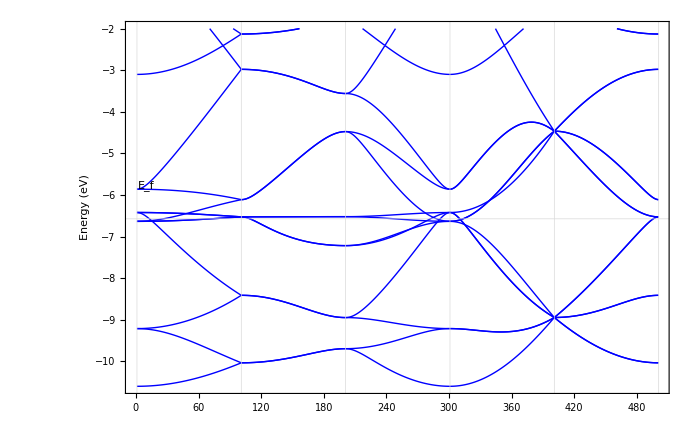

```mathematica
(*6. 计算能谱*)
energyData=Table[Sort[Re[Eigenvalues[Ham@@k]]],{k,kPath}];
(*费米能级 (假设每个 H 原子贡献 1 个电子，总电子数为 12)*)(*总共 48 条带，占据最低的 12/2=6 条带(考虑自旋)*)(*或者如果不考虑自旋，就是前 12 条带*)
nElectrons=12;
vbm=Max[energyData[[All,nElectrons/2]]]
cbm=Min[energyData[[All,nElectrons/2+1]]]
Ef=(vbm+cbm)/2

(*画图*)
ListLinePlot[
Transpose[energyData],
PlotRange->{Min[energyData],-2},
Frame->True,
Axes->False(*这里的 False 确保不会因为坐标轴重合而出现 y=0 的实线*),
GridLines->{Table[i*segments+1,{i,0,5}],{Ef}},
GridLinesStyle->{Directive[Gray,Dashed],Directive[Red,Thick,Dashed]},
(*PlotStyle->Table[If[i<=nElectrons/2,Blue,Red],{i,48}],*) (*占据态蓝色，空态红色*)
PlotStyle->Directive[Thick,Blue],FrameLabel->{None,"Energy (eV)"},

Epilog->{Style[Text["\!\(\*SubscriptBox[\(E\), \(f\)]\)",{10,Ef+0.8}],Black,14,Bold]}]
```

```mathematica
(* ===Gamma 点能级与简并度分析===*)gammaK={0,0,0};
(*计算 Gamma 点的哈密顿矩阵并求特征值*)
gammaHam=Ham@@gammaK;
gammaEvals=Sort[Re[Eigenvalues[gammaHam]]];

(*设置数值容差，用于判断能级是否简并*)
tol=10^-5;

(*使用 Tally 统计简并度：如果两个能量差值小于 tol，则视为简并*)
tallyData=Tally[gammaEvals,Abs[#1-#2]<tol&];

(*按能量从低到高排序*)
sortedTally=SortBy[tallyData,First];

Print["\n--- Gamma 点能级简并度分析 ---"];
Print[TableForm[MapAt[NumberForm[#,{Infinity,6}]&,sortedTally,{All,1}],TableHeadings->{None,{"能量 (eV)","简并度"}}]];

(*可选：打印总能级数验证*)
Print["总能级数 (含简并): ",Total[sortedTally[[All,2]]]];
```

{-10.6,-9.21253,-9.21253,-6.63357,-6.63357,-6.63357,-6.42091,-6.42091,-6.42091,-5.8606,-5.8606,-3.1,-0.989602,-0.989602,-0.989602,-0.55,-0.55,-0.55,-0.55,-0.55,-0.55,-0.289602,-0.289602,-0.289602,0.6,2.93357,2.93357,2.93357,3.1106,3.1106,4.12091,4.12091,4.12091,4.2896,4.2896,4.2896,4.55,4.55,4.55,4.55,4.55,4.55,4.9896,4.9896,4.9896,5.96253,5.96253,7.1}

--- Gamma 点能级简并度分析 ---

能量 (eV) | 简并度
-10.600000 | 1
-9.212531 | 2
-6.633566 | 3
-6.420911 | 3
-5.860602 | 2
-3.100000 | 1
-0.989602 | 3
-0.550000 | 6
-0.289602 | 3
0.600000 | 1
2.933566 | 3
3.110602 | 2
4.120911 | 3
4.289602 | 3
4.550000 | 6
4.989602 | 3
5.962531 | 2
7.100000 | 1

总能级数 (含简并): 48